```mathematica
(*css zebrafinch model*)
(*recursions*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsO) vI z +lsO qO ) + nh vh((1-lhO) vI z +lhO qO );
NNn :=ns vs((1-lsO) vI (1-z)+lsO(1- qO) ) + nh vh((1-lhO) vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsO) vI z +lsO qO ), vh((1-lhO) vI z +lhO qO ), 0, 0}, {vs((1-lsO) vI (1-z)+lsO(1- qO) ), vh((1-lhO) vI (1-z)+lhO(1- qO) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa]
```

{{Fa→(bn lhO u vh-bn lhO pn u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn u vs+bn pn vI vs-bn lsO pn vI vs-ba vh vI z+bn vh vI z+ba lhO vh vI z-bn lhO vh vI z+ba pa vh vI z-ba lhO pa vh vI z-bn pn vh vI z+bn lhO pn vh vI z-ba pa vI vs z+ba lsO pa vI vs z+bn pn vI vs z-bn lsO pn vI vs z-√(-4 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs) (bn vh vI z-bn lhO vh vI z-bn pn vh vI z+bn lhO pn vh vI z+bn pn vI vs z-bn lsO pn vI vs z)+(-bn lhO u vh+bn lhO pn u vh-bn vh vI+bn lhO vh vI+bn pn vh vI-bn lhO pn vh vI-bn lsO pn u vs-bn pn vI vs+bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z)^2))/(2 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs))},{Fa→(bn lhO u vh-bn lhO pn u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn u vs+bn pn vI vs-bn lsO pn vI vs-ba vh vI z+bn vh vI z+ba lhO vh vI z-bn lhO vh vI z+ba pa vh vI z-ba lhO pa vh vI z-bn pn vh vI z+bn lhO pn vh vI z-ba pa vI vs z+ba lsO pa vI vs z+bn pn vI vs z-bn lsO pn vI vs z+√(-4 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs) (bn vh vI z-bn lhO vh vI z-bn pn vh vI z+bn lhO pn vh vI z+bn pn vI vs z-bn lsO pn vI vs z)+(-bn lhO u vh+bn lhO pn u vh-bn vh vI+bn lhO vh vI+bn pn vh vI-bn lhO pn vh vI-bn lsO pn u vs-bn pn vI vs+bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z)^2))/(2 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs))}}

```mathematica
test = {lsO-> 0.2 ,lhO-> 0.8};
subs = {ba->3,bn->1,z->0.8,vs->0.4,vh->0.9,vI->0.8  ,u->0.1, pa-> 0, pn-> 1};
```

```mathematica
Fasols[[1,1,2]]/.subs/.test (*check it is stable qhat with values, select positive q-hat*)
 Fasols/.subs
```

0.587291

{{Fa→(-1.152+1.728 lhO-√(-4 (-1.84+1.89 lhO-0.28 lsO) (0.256-0.256 lsO)+(1.152-1.728 lhO+0.536 lsO)^2)-0.536 lsO)/(2 (-1.84+1.89 lhO-0.28 lsO))},{Fa→(-1.152+1.728 lhO+√(-4 (-1.84+1.89 lhO-0.28 lsO) (0.256-0.256 lsO)+(1.152-1.728 lhO+0.536 lsO)^2)-0.536 lsO)/(2 (-1.84+1.89 lhO-0.28 lsO))}}

```mathematica
QHAT= Simplify[Fasols[[1,1,2]]];
```

```mathematica
AA2=Simplify[AA/.{Na->QH,Nn->(1-QH)}/.subs];
```

```mathematica
LL=Eigenvalues[AA2];
```

```mathematica
LL
```

{Root[2.08167×10^-17-0.6912 lhO+0.6912 lsO+8.32667×10^-17 lhO lsO+0.7776 lhO QH-0.7776 lsO QH-1.66533×10^-16 lhO lsO QH+(-1.792+1.728 lhO-0.336 lsO-2.43 lhO QH+0.36 lsO QH) #1^2+1. #1^4&,1],Root[2.08167×10^-17-0.6912 lhO+0.6912 lsO+8.32667×10^-17 lhO lsO+0.7776 lhO QH-0.7776 lsO QH-1.66533×10^-16 lhO lsO QH+(-1.792+1.728 lhO-0.336 lsO-2.43 lhO QH+0.36 lsO QH) #1^2+1. #1^4&,2],Root[2.08167×10^-17-0.6912 lhO+0.6912 lsO+8.32667×10^-17 lhO lsO+0.7776 lhO QH-0.7776 lsO QH-1.66533×10^-16 lhO lsO QH+(-1.792+1.728 lhO-0.336 lsO-2.43 lhO QH+0.36 lsO QH) #1^2+1. #1^4&,3],Root[2.08167×10^-17-0.6912 lhO+0.6912 lsO+8.32667×10^-17 lhO lsO+0.7776 lhO QH-0.7776 lsO QH-1.66533×10^-16 lhO lsO QH+(-1.792+1.728 lhO-0.336 lsO-2.43 lhO QH+0.36 lsO QH) #1^2+1. #1^4&,4]}

```mathematica
LV=Eigenvectors[AA2]
```

{{1./Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,1],-((0.444444 (-0.177778-0.933333 lsO+1. lsO QH+2.77778 Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,1]^2))/((-0.177778-0.933333 lhO+1. lhO QH) Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,1])),-1/(-0.177778-0.933333 lhO+1. lhO QH)0.148148 (-0.177778-0.933333 lsO+1. lsO QH+2.77778 Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,1]^2),1.},{1./Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,2],-((0.444444 (-0.177778-0.933333 lsO+1. lsO QH+2.77778 Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,2]^2))/((-0.177778-0.933333 lhO+1. lhO QH) Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,2])),-1/(-0.177778-0.933333 lhO+1. lhO QH)0.148148 (-0.177778-0.933333 lsO+1. lsO QH+2.77778 Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,2]^2),1.},{1./Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,3],-((0.444444 (-0.177778-0.933333 lsO+1. lsO QH+2.77778 Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,3]^2))/((-0.177778-0.933333 lhO+1. lhO QH) Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,3])),-1/(-0.177778-0.933333 lhO+1. lhO QH)0.148148 (-0.177778-0.933333 lsO+1. lsO QH+2.77778 Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,3]^2),1.},{1./Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,4],-((0.444444 (-0.177778-0.933333 lsO+1. lsO QH+2.77778 Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,4]^2))/((-0.177778-0.933333 lhO+1. lhO QH) Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,4])),-1/(-0.177778-0.933333 lhO+1. lhO QH)0.148148 (-0.177778-0.933333 lsO+1. lsO QH+2.77778 Root[-0.28444444444444 lhO+0.28444444444444 lsO+0.32 lhO QH-0.32 lsO QH+(-0.73744855967078+0.71111111111111 lhO-0.13827160493827 lsO-1. lhO QH+0.14814814814815 lsO QH) #1^2+0.41152263374486 #1^4&,4]^2),1.}}

```mathematica
LL/.subs /.test /.QH-> 0.5  (*sub in rando qhat value to identify positive eigen values*)
```

{-1.23745,1.23745,0.-0.344222 ⅈ,0.+0.344222 ⅈ}

```mathematica
(*eigenvectors give one ratios of stage/stress classes*) 
LV/.subs /.test /.QH-> 0.5
```

{{-0.808112,-2.73192,1.12687,1.},{0.808112,2.73192,1.12687,1.},{0.+2.90511 ⅈ,0.-1.46136 ⅈ,-0.167678+0. ⅈ,1.},{0.-2.90511 ⅈ,0.+1.46136 ⅈ,-0.167678+0. ⅈ,1.}}

```mathematica
LL2=LL[[2]]/.QH ->QHAT;
```

```mathematica
(*isolate dominant eigenvalue*)
Lambda[ lsO_, lhO_]:=LL2
```

```mathematica
(*use Lambda1 for general soln with pa and pn as parameters*)
DlsO=D[Lambda[lsO, lhO],lsO]/.subs;
```

```mathematica
DlhO=D[Lambda[lsO, lhO],lhO] /.subs;
```

```mathematica
(*try and graph*)

lsOstart=0.01;
lhOstart=0.01;
imax=1000;
lsItab=Table[0,{i,imax}];
lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.04;
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;

DlsOtab[[1]]=DlsO/.subs/.{lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.subs/.{lsO->lsOstart,lhO->lhOstart};
```

```mathematica
For[i=2,i<imax,i++,{

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsOtab[[i]]=DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];
```

```mathematica
lsItab = 1-lsOtab;
lhItab = 1-lhOtab;
```

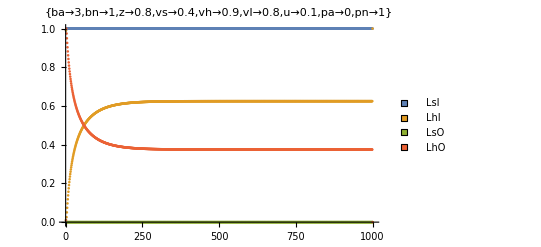

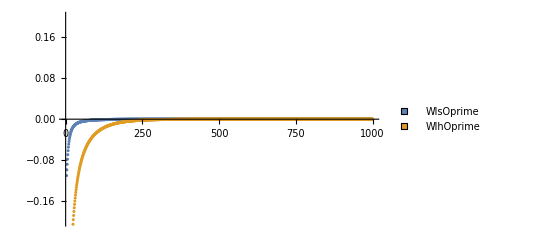

```mathematica
ListPlot[{lsItab,lhItab,lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLabel->subs, PlotLegends->PointLegend[{LsI,LhI,LsO,LhO},LegendMarkers->Graphics[Rectangle[]]]] 
ListPlot[{DlsOtab,DlhOtab},PlotRange->{All,{-0.2,0.2}},PlotLegends->PointLegend[{WlsOprime,WlhOprime},LegendMarkers->Graphics[Rectangle[]]]]
```